```mathematica
html=Import["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\mainpage.txt","Text"];
```

```mathematica
teams=StringCases[html,"<a href=http://www.ultianalytics.com/team/"~~x:Shortest[__]~~"/main-classic\">"~~y:Shortest[__]~~"</a>":>{x,y}];
```

```mathematica
{}
```

{}

```mathematica
{}
```

{}

```mathematica
ids=teams⟦All,1⟧;
```

```mathematica
{}
```

{}

```mathematica
%424
```

{5762298832486400,5199348879065088,5104011879383040,5634601401712640,5688687119564800,5173627930542080,5646521009700864,5672188833169408,5719707252424704,5701394610782208,5658753101725696,5736577883963392,5672878150254592,5767202099691520,5700228501995520,5666961832804352,5721191432060928,5740216795004928,5712818124881920,5654595548217344,5655358173347840,5753798823772160,5707300165648384,5711261467672576,5664284977659904,5128666635829248,5640136574369792,5691616589250560,5069252692279296,5705148370255872,5206956054675456,5769906008096768,5201331526565888,5723974822526976,4919856549855232,5114556594520064,5142198416834560,5686487861428224,5749730717990912,5632202645700608,5153306812874752,5675918433452032,5758196635402240,5199033182191616,5664810037411840,5743365039587328,5716256766296064,4860723440123904,5764281479987200,6327231433408512,5708939920408576,5643517367943168,5671536392404992,5674069752020992,5635093192245248,5738275486564352,5724822843686912,5633494390669312,5118639615246336,5070544437248000,5683257223938048,5753050442498048,5705718560718848,5704221898833920,5751646390845440,5641462360309760,5651757665353728,5684793748488192,5670377556541440,5734743547052032,5758048710688768,5722152447770624,5681589568667648,5754980359208960,5701751084679168,5471866718257152,5732910535540736,4868028676177920,5684961520648192,5075454121738240,5182111044599808,5638404075159552,5753341694967808,6220853180104704,5663684521099264,5682238511382528,5662069344960512,5094953273262080,6597766625099776,5648334039547904,5131065358286848,6226234774126592}

```mathematica
importTeam[{id_,name_}]:=Module[{data,keys},
data=Import["http://www.ultianalytics.com/team/"<>id<>""];
keys=data⟦1⟧;
Dataset[Association[Thread[keys⟦;;Min[Length[#],52]⟧->#⟦;;Min[Length[#],52]⟧]]&/@Drop[data,1]][All,<|"ID"->id,"Name"->name,#|>&]
]
```

```mathematica
i=0;
SetSharedVariable[i];
PrintTemporary[Dynamic[{ProgressIndicator[i/Length[teams]],i}]];
teamDatasets=ParallelMap[(PrintTemporary[++i];importTeam[#])&,teams];
CloseKernels[];
```

ParallelCombine::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
allData=Join@@teamDatasets;
```

```mathematica
(* DumpSave["C:\\Users\\praha\\Documents\\data\\dataset.mx",allData]; *)
```

```mathematica
Get["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\dataset\\dataset.mx"];
```

```mathematica
FirstPosition[Normal@allData,_?(Length[#]>50&)]
```

{31653}

```mathematica
Complement[Normal@Keys[allData[31653]],Normal@Keys[allData[450601]]]
```

{Absolute Distance,Begin Area,Begin X,Begin Y,Distance Unit of Measure,End Area,End X,End Y,Lateral Distance,Toward Our Goal Distance}

```mathematica
allData[3000,{"Date/Time"->DateObject,"Point Elapsed Seconds"->(Quantity[#,"Seconds"]&),"Absolute Distance"->(Quantity[#,"Yards"]&),"Lateral Distance" ->(Quantity[#,"Yards"]&),"Hang Time (secs)"->(Quantity[#,"Seconds"]&),"Toward Our Goal Distance"->(Quantity[#,"Yards"]&),"Elapsed Time (secs)"->(Quantity[#,"Seconds"]&)}]
```

```mathematica
allDataUniform=allData[All,If[Length[#]==54,#,Join[#,<|"Absolute Distance"->Missing[],"Begin Area"->Missing[],"Begin X"->Missing[],"Begin Y"->Missing[],"Distance Unit of Measure"->Missing[],"End Area"->Missing[],"End X"->Missing[],"End Y"->Missing[],"Lateral Distance"->Missing[],"Toward Our Goal Distance"->Missing[]|>]]&]
```

Dataset[<>]

```mathematica
curatedData=
allDataUniform[All,{"Date/Time"->DateObject,"Point Elapsed Seconds"->(Quantity[#,"Seconds"]&),"Absolute Distance"->(If[MissingQ[#],#,Quantity[#,"Yards"]]&),"Lateral Distance" ->(If[MissingQ[#],#,Quantity[#,"Yards"]]&),"Hang Time (secs)"->(Quantity[#,"Seconds"]&),"Toward Our Goal Distance"->(If[MissingQ[#],#,Quantity[#,"Yards"]]&),"Elapsed Time (secs)"->(Quantity[#,"Seconds"]&)}];
(* DumpSave["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\datasetulti.mx",curatedData]; *)
```

```mathematica
datasetulti= KeyDrop[curatedData,"Distance Unit of Measure"];
```

```mathematica
DumpSave["C:\\Users\\User 1\\Documents\\Final-Project-Kacham\\datasetulti.mx",datasetulti];
```

```mathematica
(* Compare Point Elapsed Seconds 2017 teams *)
Normal[datasetulti[1]]
```

```mathematica
<|"ID"->"5762298832486400","Name"->"Atlanta Hustle","Date/Time"->DateObject[{2017,5,27,18,58},"Minute","Gregorian",-7.],"Tournamemnt"->"","Opponent"->"Jacksonville Cannons","Point Elapsed Seconds"->Quantity[45, "Seconds"],"Line"->"D","Our Score - End of Point"->0,"Their Score - End of Point"->1,"Event Type"->"Defense","Action"->"Pull","Passer"->"","Receiver"->"","Defender"->"Lally","Hang Time (secs)"->Quantity[7.007, "Seconds"],"Player 0"->"JP Burns","Player 1"->"Trenton","Player 2"->"Lally","Player 3"->"Kelvin","Player 4"->"Staber","Player 5"->"Parker","Player 6"->"C Olsen","Player 7"->"","Player 8"->"","Player 9"->"","Player 10"->"","Player 11"->"","Player 12"->"","Player 13"->"","Player 14"->"","Player 15"->"","Player 16"->"","Player 17"->"","Player 18"->"","Player 19"->"","Player 20"->"","Player 21"->"","Player 22"->"","Player 23"->"","Player 24"->"","Player 25"->"","Player 26"->"", "Player 27"->"","Elapsed Time (secs)"->Quantity[0, "Seconds"],"Absolute Distance"->Missing[],"Begin Area"->Missing[],"Begin X"->Missing[],"Begin Y"->Missing[],"End Area"->Missing[],"End X"->Missing[],"End Y"->Missing[],"Lateral Distance"->Missing[],"Toward Our Goal Distance"->Missing[]|>
```

```mathematica
Query[2 ;; 3]@datasetulti
```

Dataset[<>]

```mathematica
Length[datasetulti]
```

450601

```mathematica
datasetulti[25 ;; 50,6]
```

Dataset[<>]

```mathematica
(* Comparing Point Elapsed Seconds 2014 - 2017 teams *)
(* What does that mean: *)
```

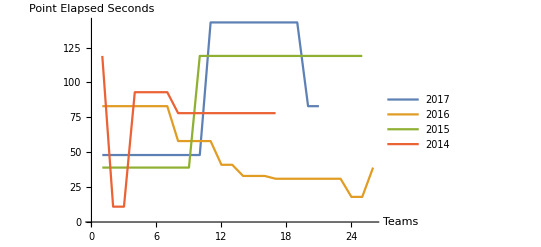

```mathematica
data1 = datasetulti[4 ;;24,6];
data2 = datasetulti[25 ;; 50,6];
data3 = datasetulti[51;; 75,6];
data4 = datasetulti[76;; 92,6];
ListLinePlot[{data1, data2,data3,data4},PlotLegends->{"2017","2016","2015","2014"},AxesLabel->{"Teams","Point Elapsed Seconds"}]
```